# Уравнения движения точки по гладкой сферической поверхности

Параметры по умолчанию для оформления графиков

```mathematica
SetOptions[Plot,AspectRatio->1,Frame->True,GridLines->Automatic,BaseStyle->14,PlotTheme->{"Web","FrameGrid"}];SetOptions[ParametricPlot,AspectRatio->1,Frame->True,GridLines->Automatic,BaseStyle->14,PlotTheme->{"Web","FrameGrid"}];
```

## Уравнения в избыточных координатах

```mathematica
params={m->1,r->1,g->9.807};
```

### Динамические уравнения системы, освобожденной от связей

Уравнения движения материальной точки, освобожденной от связей, под действием активной силы веса и силы реакции связи

```mathematica
eq={
m x''[t]==Rn[t] x[t]/r,
m y''[t]==Rn[t] y[t]/r-m g
}
```

{m x''[t]==(Rn[t] x[t])/r,m y''[t]==-g m+(Rn[t] y[t])/r}

### Уравнение связи

Точка движется по окружности (расстояние до начала координат должно быть равно r)

```mathematica
cEq=x[t]^2+y[t]^2==r^2
```

x[t]^2+y[t]^2==r^2

Первая производная уравнения связи (связь на скорости точки)

```mathematica
dcEq=D[cEq,t]//FullSimplify
```

x[t] x'[t]+y[t] y'[t]==0

Вторая производная уравнения связи (связь на ускорения точки)

```mathematica
d2cEq=D[dcEq,t]//FullSimplify
```

x'[t]^2+y'[t]^2+x[t] x''[t]+y[t] y''[t]==0

### Система дифференциально-алгебраических уравнений

ДАУ индекса 3

```mathematica
eqDAE={eq,cEq}//Flatten
```

{m x''[t]==(Rn[t] x[t])/r,m y''[t]==-g m+(Rn[t] y[t])/r,x[t]^2+y[t]^2==r^2}

```mathematica
sol1=NDSolve[{eqDAE,x[0]==r Cos[80°],y[0]==r Sin[80°],x'[0]==0,y'[0]==0}/.params,
{x[t],y[t],Rn[t],x'[t],y'[t]},{t,0,20},Method->{"IndexReduction"->Automatic}]//Flatten;
```

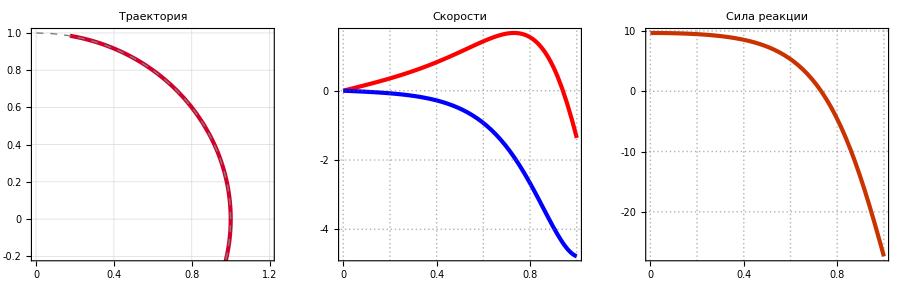

```mathematica
ParametricPlot[{x[t],y[t]}/.sol1,{t,0,1},PlotRange->{{0,1.2},{-0.2,1}},ColorFunction->Function[{x,y,u,v},If[Rn[t]>0/.sol1/.t->u,Blue,Red]],ColorFunctionScaling->False];
GraphicsRow[{
Show[%,Graphics[{Gray,Dashed,Circle[{0,0},1]}],PlotLabel->"Траектория"],
Plot[{x'[t],y'[t]}/.sol1//Evaluate,{t,0,1},PlotStyle->{Red,Blue},PlotLabel->"Скорости"],
Plot[Rn[t]/.sol1,{t,0,1},PlotLabel->"Сила реакции"]
},ImageSize->900]
```

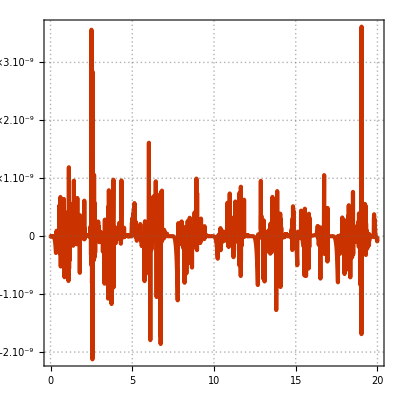

```mathematica
Plot[x[t]^2+y[t]^2-1/.sol1,{t,0,20},PlotRange->All]
```

#### ДАУ индекса 1

```mathematica
eqDAE={eq,d2cEq}//Flatten;
sol1=NDSolve[
{eqDAE,x[0]==r Cos[80°],y[0]==r Sin[80°],x'[0]==0,y'[0]==0}/.params,
{x[t],y[t],Rn[t],x'[t],y'[t]},
{t,0,20},
Method->{"IndexReduction"->Automatic}]//Flatten;
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

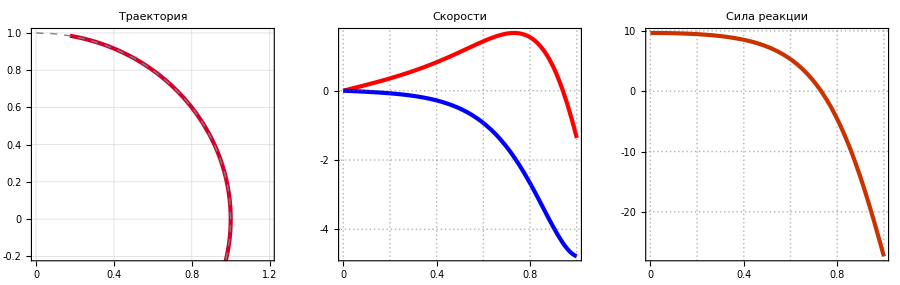

```mathematica
ParametricPlot[{x[t],y[t]}/.sol1,{t,0,1},PlotRange->{{0,1.2},{-0.2,1}},ColorFunction->Function[{x,y,u,v},If[Rn[t]>0/.sol1/.t->u,Blue,Red]],ColorFunctionScaling->False];
GraphicsRow[{
Show[%,Graphics[{Gray,Dashed,Circle[{0,0},1]}],PlotLabel->"Траектория"],
Plot[{x'[t],y'[t]}/.sol1//Evaluate,{t,0,1},PlotStyle->{Red,Blue},PlotLabel->"Скорости"],
Plot[Rn[t]/.sol1,{t,0,1},PlotLabel->"Сила реакции"]
},ImageSize->900]
```

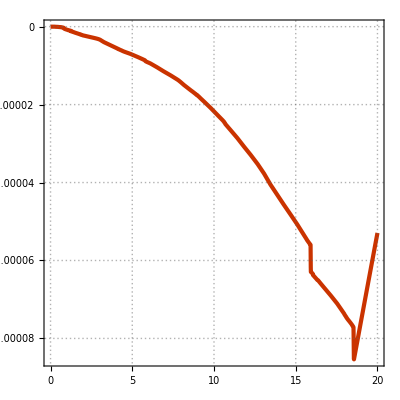

```mathematica
Plot[x[t]^2+y[t]^2-1/.sol1,{t,0,20},PlotRange->All]
```

```mathematica
eqDAE={eq,d2cEq}//Flatten
eqDAE2={eq,Rn[t]==0}//Flatten
```

{m x''[t]==(Rn[t] x[t])/r,m y''[t]==-g m+(Rn[t] y[t])/r,x'[t]^2+y'[t]^2+x[t] x''[t]+y[t] y''[t]==0}

{m x''[t]==(Rn[t] x[t])/r,m y''[t]==-g m+(Rn[t] y[t])/r,Rn[t]==0}

```mathematica
sol1=NDSolve[{eqDAE,WhenEvent[Rn[t]<0,"StopIntegration"],x[0]==r Cos[80°],y[0]==r Sin[80°],x'[0]==0,y'[0]==0}/.params,
{x[t],y[t],Rn[t],x'[t],y'[t]},{t,0,1}]//Flatten;
t1=sol1[[1,2,0,1,1,2]];

sol2=NDSolve[{eqDAE2,
{x[t1]==x[t],y[t1]==y[t],x'[t1]==x'[t],y'[t1]==y'[t]}/.sol1/.t->t1}/.params,
{x[t],y[t],Rn[t],x'[t],y'[t]},{t,t1,1}]//Flatten;
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

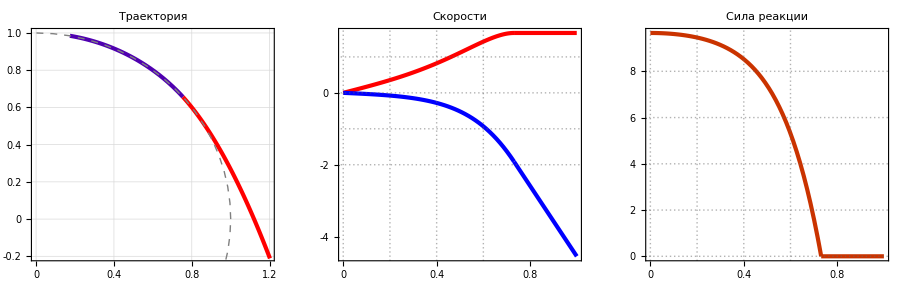

```mathematica
ParametricPlot[{x[t],y[t]}/.sol1,{t,0,t1},PlotRange->{{0,1.2},{-0.2,1}},ColorFunction->Function[{x,y,u,v},If[Rn[t]>0/.sol1/.t->u,Blue,Red]],ColorFunctionScaling->False];
ParametricPlot[{x[t],y[t]}/.sol2,{t,t1,1},PlotRange->{{0,1.2},{-0.2,1}},ColorFunction->Function[{x,y,u,v},If[Rn[t]>0/.sol2/.t->u,Blue,Red]],ColorFunctionScaling->False];
GraphicsRow[{
Show[%,%%,Graphics[{Gray,Dashed,Circle[{0,0},1]}],PlotLabel->"Траектория"],
Show[
Plot[{x'[t],y'[t]}/.sol1//Evaluate,{t,0,t1},PlotStyle->{Red,Blue},PlotLabel->"Скорости"],
Plot[{x'[t],y'[t]}/.sol2//Evaluate,{t,t1,1},PlotStyle->{Red,Blue},PlotLabel->"Скорости"],
PlotRange->{{0,1},Automatic}
],
Show[
Plot[Rn[t]/.sol1,{t,0,t1},PlotLabel->"Сила реакции"],
Plot[Rn[t]/.sol2,{t,t1,1},PlotLabel->"Сила реакции"],
PlotRange->{{0,1},Automatic}
]
},ImageSize->900]
```

## Уравнения Лагранжа

```mathematica
V=D[r{Cos[φ[t]],Sin[φ[t]]},t]
```

{-r Sin[φ[t]] φ'[t],r Cos[φ[t]] φ'[t]}

```mathematica
T=m V.V/2//FullSimplify
```

1/2 m r^2 φ'[t]^2

```mathematica
eqL=D[D[T,φ'[t]],t]-D[T,φ[t]]==-D[m g r Sin[φ[t]],φ[t]]
```

m r^2 φ''[t]==-g m r Cos[φ[t]]

```mathematica
solL=NDSolve[{eqL,φ[0]==80°,φ'[0]==0}/.params,{φ[t],φ'[t]},{t,0,1}]//Flatten;
```

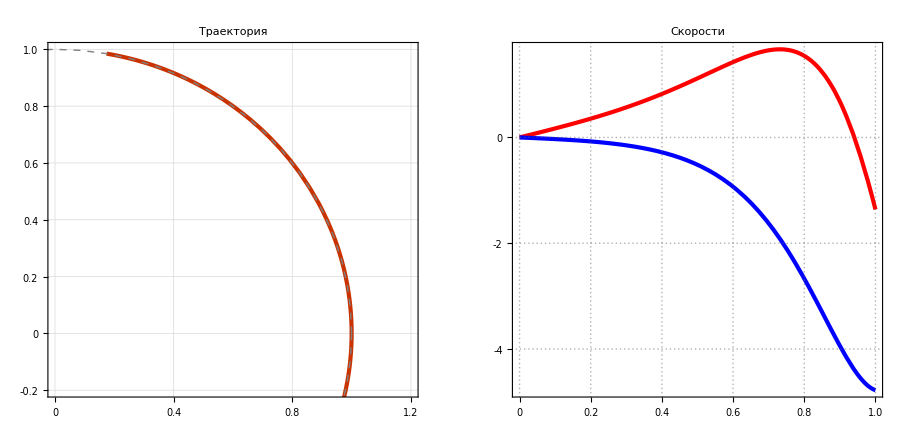

```mathematica
ParametricPlot[r{Cos[φ[t]],Sin[φ[t]]}/.params/.solL,{t,0,1},PlotRange->{{0,1.2},{-0.2,1}}];
GraphicsRow[{
Show[%,Graphics[{Gray,Dashed,Circle[{0,0},1]}],PlotLabel->"Траектория"],
Plot[V/.params/.solL//Evaluate,{t,0,1},PlotStyle->{Red,Blue},PlotLabel->"Скорости"]
},ImageSize->900]
```